```mathematica
V2[r,Fc,Fd]
```

-1/r-(0.99895352636201278972478862820538575868617674167672 ⅇ^(-0.99829411813147086629445907603814099626336482661085 r))/r

## Definition

```mathematica
δ50V
```

{-0.0010112856325842592115757959830257288769174312661043,-0.0031979514080297200565705801369439080855768479834806,-0.010112350006745220481854887244857385967687882933032,-0.031963506093170159583209457326136242978196319440701,-0.10061832202777640843855402875546789112115337853744,-0.30404492419226639325731867851940898130237936605025,-0.73218616812544429244691233908324449275329261079977,1.5707021615698040610795795427416257288624199775951,0.016557513202545089012814437925417763745229506340837,-0.88675415738537435657903073228779345656203834738601,-0.20308391623460119181902399902605579493281184899885,0.68192921824636007063061608809441586528321902791818,-0.14542598704360428938800819766848074673728862597987,0.55956397156694773124628350106136995203978741529876,-1.0399695656655053202848978086311236182759088446379,1.513792052208833237509271410950095093049494771153,0.011514653577586000833403492611989732072880873646496,-0.85176835394692940384579023395535525903163621248286,-1.1461212573699322468795765796113703665761075661832}

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=1;αSch=2m;
a=1;ee={10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1,3,7,10};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V1[r_,Fa_]=-α/r+If[0≤r<a,Fa,0];
V2[r_,Fc_,Fd_]=-α/r+Fc E^(-Fd r)/r;
V3[r_,Fe_,Fh_]=-α/r+Fe(E^(-Fh r^2))/r;
```

```mathematica
Fc=-0.99895352636201278972478862820538575868617674167672469199326097337382722470925`50.;
Fd=0.99829411813147086629445907603814099626336482661084574202538457473067509617705`50.;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[evShifted[[n]],3],1.01 SetPrecision[evShifted[[n]],3]},opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
(*PrintTemporary[{estart,eend}];*)
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2(*,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}*)]]
```

```mathematica
δexpminus10=δ50e[10^-10,V2[r,Fc,Fd]];
δexpminus5=δ50e[10^-5,V2[r,Fc,Fd]];
δ50V=δ50[V2[r,Fc,Fd]];
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031979675285863811032093311326522213716570452313) is less than WorkingPrecision (50.).

End with 0.2812420s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095925761813024790965822583220900869642847802) is less than WorkingPrecision (50.).

End with 0.2500195s

NDSolve::precw: The precision of the differential equation ({{2 (0.01+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112859773312107943129835816740420171167336579) is less than WorkingPrecision (50.).

End with 0.2612295s

{1/1000000000,-0.0010112856325842592115757959830257288769174312661043}    0.276855

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031974395882989441335467147824253540611591509037) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.898862) is less than WorkingPrecision (50.).

End with 0.3081041s

End with 0.3071027s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22644) is less than WorkingPrecision (50.).

{1/1000000,-0.031963506093170159583209457326136242978196319440701}    0.308104

{0.001,-0.73218616812544429244691233908324449275329261079977}    0.307103

End with 0.3696030s

NDSolve::precw: The precision of the differential equation ({{2 (0.003+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.01,-0.88675415738537435657903073228779345656203834738601}    0.369603

NDSolve::precw: The precision of the differential equation ({{2 (0.03+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031979623097768280183235420630813191103322660897) is less than WorkingPrecision (50.).

End with 0.3125014s

{1/100000000,-0.0031979514080297200565705801369439080855768479834806}    0.312501

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095925761813024790965822583220900869642847802) is less than WorkingPrecision (50.).

End with 0.3593907s

{1/100000,-0.10061832202777640843855402875546789112115337853744}    0.375003

FindRoot::precw: The precision of the argument function (Tan[δ]==10619.6) is less than WorkingPrecision (50.).

End with 0.4531283s

{0.003,1.5707021615698040610795795427416257288624199775951}    0.453128

NDSolve::precw: The precision of the differential equation ({{2 (0.007+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010112694715877119214533810749472540592431032704) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.205923) is less than WorkingPrecision (50.).

End with 0.2812522s

End with 0.5312549s

{1/10000000,-0.010112350006745220481854887244857385967687882933032}    0.296878

{0.03,-0.20308391623460119181902399902605579493281184899885}    0.531255

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31377380486608449328418970819913870802281123877) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.3+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.07+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 0.3125162s

{1/10000,-0.30404492419226639325731867851940898130237936605025}    0.328128

FindRoot::precw: The precision of the argument function (Tan[δ]==0.016559) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.3750050s

{0.007,0.016557513202545089012814437925417763745229506340837}    0.375005

FindRoot::precw: The precision of the argument function (Tan[δ]==0.811857) is less than WorkingPrecision (50.).

End with 0.5937425s

{0.07,0.68192921824636007063061608809441586528321902791818}    0.593743

NDSolve::precw: The precision of the differential equation ({{2 (0.1+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.626342) is less than WorkingPrecision (50.).

End with 0.7343682s

{0.3,0.55956397156694773124628350106136995203978741529876}    0.749994

NDSolve::precw: The precision of the differential equation ({{2 (0.7+1/r+0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.14646) is less than WorkingPrecision (50.).

End with 0.6093806s

{0.1,-0.14542598704360428938800819766848074673728862597987}    0.609381

FindRoot::precw: The precision of the argument function (Tan[δ]==17.52353854324885975009478330829739009032434193) is less than WorkingPrecision (50.).

End with 1.1875105s

{1,1.513792052208833237509271410950095093049494771153}    1.203136

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.7035) is less than WorkingPrecision (50.).

End with 0.9375099s

{0.7,-1.0399695656655053202848978086311236182759088446379}    0.9375099

FindRoot::precw: The precision of the argument function (Tan[δ]==0.011515162503316224764152623099056632622698676) is less than WorkingPrecision (50.).

End with 1.6396790s

{3,0.011514653577586000833403492611989732072880873646496}    1.655303

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.1424006956231355724951564171636785974873306041) is less than WorkingPrecision (50.).

End with 3.0615704s

{7,-0.85176835394692940384579023395535525903163621248286}    3.092806

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.211451356348885920676828792057387912342071735) is less than WorkingPrecision (50.).

End with 2.5839888s

{10,-1.1461212573699322468795765796113703665761075661832}    2.615223

## FindFit For Lepage’s Data

```mathematica
Clear[Fc,Fd]
```

```mathematica
enDetermineFcd[Fc_?NumberQ,Fd_?NumberQ,enF_]:=EigenEnergySolo[V2[r,Fc,Fd],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[enF],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
EvaluateV2[Fc_,Fd_]:=((enDetermineFcd[Fc,Fd,#]-#)&/@{-0.00129205010,-0.00534541931});
FindRoot[(enDetermineFcd[Fc,Fd,#]==#)&/@{-0.00129205010,-0.00534542},{{Fc,-0.9,-1.1},{Fd,0.9,1.1}},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{{Fc,Fd},EvaluateV2[Fc,Fd]}]]
```

FindRoot::precw: The precision of the argument function ({enDetermineFcd[Fc,Fd,-0.00129205]==-0.00129205,enDetermineFcd[Fc,Fd,-0.00534542]==-0.00534542}) is less than WorkingPrecision (50.).

-1/r-(0.9 ⅇ^(-0.9 r))/r

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.9 Power[«2»] Power[«2»]) u[r$3113]-u''[r$3113]/2==e$3112 u[r$3113],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

-1/r-(0.9 ⅇ^(-0.9 r))/r

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.9 Power[«2»] Power[«2»]) u[r$4277]-u''[r$4277]/2==e$4276 u[r$4277],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

-1/r-(1.1 ⅇ^(-0.9 r))/r

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.1 Power[«2»] Power[«2»]) u[r$5360]-u''[r$5360]/2==e$5359 u[r$5360],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

-1/r-(1.1 ⅇ^(-0.9 r))/r

-1/r-(1.1 ⅇ^(-1.1 r))/r

-1/r-(1.1 ⅇ^(-1.1 r))/r

-1/r-(1.1 ⅇ^(-1.1 r))/r

«1 more identical outputs»

-1/r-(1.01263 ⅇ^(-1.01744 r))/r

-1/r-(1.01263 ⅇ^(-1.01744 r))/r

-1/r-(1.01263 ⅇ^(-1.01744 r))/r

«1 more identical outputs»

{{-1.01263,1.01744},{{-7.59271×10^-8},{-6.32323×10^-7}}}

-1/r-(1.01263 ⅇ^(-1.01744 r))/r

-1/r-(1.01263 ⅇ^(-1.01744 r))/r

-1/r-(1.00648 ⅇ^(-1.00966 r))/r

-1/r-(1.00648 ⅇ^(-1.00966 r))/r

-1/r-(1.00648 ⅇ^(-1.00966 r))/r

«1 more identical outputs»

{{-1.00648,1.00966},{{-2.18983×10^-8},{-1.80386×10^-7}}}

-1/r-(1.00648 ⅇ^(-1.00966 r))/r

-1/r-(1.00648 ⅇ^(-1.00966 r))/r

-1/r-(0.999905 ⅇ^(-0.9997 r))/r

-1/r-(0.999905 ⅇ^(-0.9997 r))/r

-1/r-(0.999905 ⅇ^(-0.9997 r))/r

«1 more identical outputs»

{{-0.999905,0.9997},{{-3.48675×10^-9},{-2.9466×10^-8}}}

-1/r-(0.999905 ⅇ^(-0.9997 r))/r

-1/r-(0.999905 ⅇ^(-0.9997 r))/r

-1/r-(0.998943 ⅇ^(-0.998275 r))/r

-1/r-(0.998943 ⅇ^(-0.998275 r))/r

-1/r-(0.998943 ⅇ^(-0.998275 r))/r

«1 more identical outputs»

{{-0.998943,0.998275},{{-4.02677×10^-11},{-1.03717×10^-9}}}

-1/r-(0.998943 ⅇ^(-0.998275 r))/r

-1/r-(0.998943 ⅇ^(-0.998275 r))/r

-1/r-(0.998954 ⅇ^(-0.998296 r))/r

-1/r-(0.998954 ⅇ^(-0.998296 r))/r

-1/r-(0.998954 ⅇ^(-0.998296 r))/r

«1 more identical outputs»

{{-0.998954,0.998296},{{4.84529×10^-12},{-6.48453×10^-10}}}

-1/r-(0.998954 ⅇ^(-0.998296 r))/r

-1/r-(0.998954 ⅇ^(-0.998296 r))/r

-1/r-(0.998954 ⅇ^(-0.998294 r))/r

-1/r-(0.998954 ⅇ^(-0.998294 r))/r

-1/r-(0.998954 ⅇ^(-0.998294 r))/r

«1 more identical outputs»

{{-0.998954,0.998294},{{9.06393×10^-16},{-6.89992×10^-10}}}

-1/r-(0.9989544620892242265952631896653 ⅇ^(-0.9982958445579868111963151022792 r))/r

-1/r-(0.9989544620892242265952631896653 ⅇ^(-0.9982958445579868111963151022792 r))/r

-1/r-(0.9989430420064796534163065189205 ⅇ^(-0.998275357051708001066003816959 r))/r

-1/r-(0.9989430420064796534163065189205 ⅇ^(-0.998275357051708001066003816959 r))/r

-1/r-(0.9989535285787398688484017839073 ⅇ^(-0.9982941217751265527979853686702 r))/r

-1/r-(0.9989535285787398688484017839073 ⅇ^(-0.9982941217751265527979853686702 r))/r

-1/r-(0.9989535285787398672866468998127 ⅇ^(-0.9982941217751265499318276354418 r))/r

-1/r-(0.9989535285787398672866468998127 ⅇ^(-0.9982941217751265499318276354418 r))/r

-1/r-(0.9989535283953230776696754145017 ⅇ^(-0.9982941214385171016000157533717 r))/r

-1/r-(0.9989535283953230776696754145017 ⅇ^(-0.9982941214385171016000157533717 r))/r

-1/r-(0.9989535283953230776696754145017 ⅇ^(-0.9982941214385171016000157533717 r))/r

«1 more identical outputs»

{{-0.9989535283953230776696754145017,0.9982941214385171016000157533717},{{-2.1684×10^-19},{-6.9×10^-10}}}

-1/r-(0.9989535283953230775364439748322 ⅇ^(-0.9982941214385171013835902411215 r))/r

-1/r-(0.9989535283953230775364439748322 ⅇ^(-0.9982941214385171013835902411215 r))/r

-1/r-(0.99895352839532307766967541450171797963745925347245 ⅇ^(-0.99829412143851710160001575337166488821486007992911 r))/r

-1/r-(0.99895352839532307766967541450171797963745925347245 ⅇ^(-0.99829412143851710160001575337166488821486007992911 r))/r

-1/r-(0.99895446208922422659526318966527469456195831298828 ⅇ^(-0.998295844557986811196315102279186248779296875 r))/r

-1/r-(0.99895446208922422659526318966527469456195831298828 ⅇ^(-0.998295844557986811196315102279186248779296875 r))/r

-1/r-(0.99895352839532307766967541450171797963745925347245 ⅇ^(-0.99829412143851710160001575337166488821486007992911 r))/r

-1/r-(0.99895352839532307766967541450171797963745925347245 ⅇ^(-0.99829412143851710160001575337166488821486007992911 r))/r

-1/r-(0.99895352857873986884840178390732035040855407714844 ⅇ^(-0.99829412177512655279798536867019720375537872314453 r))/r

-1/r-(0.99895352857873986884840178390732035040855407714844 ⅇ^(-0.99829412177512655279798536867019720375537872314453 r))/r

-1/r-(0.99895352839532307766967541450103599517385592595555 ⅇ^(-0.99829412143851710160001575337055705032578446849566 r))/r

-1/r-(0.99895352839532307766967541450103599517385592595555 ⅇ^(-0.99829412143851710160001575337055705032578446849566 r))/r

-1/r-(0.99895352839414155704723073894584328766101117601336 ⅇ^(-0.99829412143659780082100307243052294796177564852075 r))/r

-1/r-(0.99895352839414155704723073894584328766101117601336 ⅇ^(-0.99829412143659780082100307243052294796177564852075 r))/r

-1/r-(0.99895352839414155704723073894584328766101117601336 ⅇ^(-0.99829412143659780082100307243052294796177564852075 r))/r

«1 more identical outputs»

{{-0.99895352839414155704723073894584328766101117601336,0.99829412143659780082100307243052294796177564852075},{{0.},{-6.9×10^-10}}}

-1/r-(0.99895352839414155704723073894621926954851098095084 ⅇ^(-0.9982941214365978008210030724311340066009544070484 r))/r

-1/r-(0.99895352839414155704723073894621926954851098095084 ⅇ^(-0.9982941214365978008210030724311340066009544070484 r))/r

-1/r-(0.99895352839450084315354463384582611896028934543834 ⅇ^(-0.99829412143718172490484638597695485543582477870271 r))/r

-1/r-(0.99895352839450084315354463384582611896028934543834 ⅇ^(-0.99829412143718172490484638597695485543582477870271 r))/r

-1/r-(0.99895352839450084315354463384582611896028934543834 ⅇ^(-0.99829412143718172490484638597695485543582477870271 r))/r

«1 more identical outputs»

{{-0.99895352839450084315354463384582611896028934543834,0.99829412143718172490484638597695485543582477870271},{{-2.1684×10^-19},{-6.9×10^-10}}}

-1/r-(0.99895352839414155704723073894617114952356777493247 ⅇ^(-0.99829412143659780082100307243105555644238167837957 r))/r

-1/r-(0.99895352839414155704723073894617114952356777493247 ⅇ^(-0.99829412143659780082100307243105555644238167837957 r))/r

-1/r-(0.99895352839441463685595309405835491853764910093797 ⅇ^(-0.99829412143704141637565664442236761757152978701529 r))/r

```mathematica
EigenEnergy[V2[r,Fc,Fd],αSch,{1.*10^-15,2000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.28671,-0.183338,-0.0703762,-0.0371497,-0.0229269,-0.0155493,-0.0112354,-0.00849649,-0.00664955,-0.00534542,-0.00439048,-0.00367033,-0.00311387,-0.00267499,-0.00232276,-0.00203579,-0.00179889,-0.00160106,-0.00143415,-0.00129204}

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r$219318]-u''[r$219318]/2==e$219317 u[r$219318],u'[2000]==-1.×10^-15,u[2000]==1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 1622.49548640481558128326657306.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 1626.24696039758772565672124926.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 1622.49548640481558128326657306.

General::stop: Further output of ParametricNDSolve::mxst will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{0.661988783551193566553974741112,-0.0877488242233913699329909875258,-0.0662804155821857341534317875243,-0.0371496991275094971376871216291,-0.0229268596243229908242861347373,-0.0155492725533467704478200973264,-0.0112354155906817963792443540493,-0.00849649511189428805344001023526,-0.00664955109448462572903939845956,-0.00534542000000000044804497862288,-0.00439047881407927901570550355666,-0.00367033290159754118667384782054,-0.00311386901560142172482786082609,-0.00267499301607192988019323757218,-0.00232276448120563406646016825862,-0.00203578877656797250950195440884,-0.00179888915074952220468132047761,-0.00160105779184532772026119297082,-0.00143415343818258176190046376664,-0.00129205009999983359076539824947}

```mathematica
EigenEnergySolo[V2[r,Fc,Fd],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-0.03714968384569772],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->1000}]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) u[r$232994]-u''[r$232994]/2==e$232993 u[r$232994],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0371496991275094971376871216291}

```mathematica
enV2[[4]]=First@%
```

-0.0371496991275094971376871216291

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_enV2.mx",enV2]
```

{{-1.28671748016823998683246939937,-0.183338515542431527686387767079,-0.0703762511086017671933385949847,-0.0371496991275094971376871216291,-0.0229268596243229908242861347373,-0.0155492725533467704478200973264,-0.0112354155906817963792443540493,-0.00849649511189428805344001023526,-0.00664955109448462572903939845956,-0.00534542000000000044804497862288,-0.00439047881407927901570550355666,-0.00367033290159754118667384782054,-0.00311386901560142172482786082609,-0.00267499301607192988019323757218,-0.00232276448120563406646016825862,-0.00203578877656797250950195440884,-0.00179888915074952220468132047761,-0.00160105779184532772026119297082,-0.00143415343818258176190046376664,-0.00129205009999983359076539824947}}

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_enV2.mx"]
```

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end_},opt___]:=Module[{aaa,findroot},aaa=a;
Print["a=",aaa];
findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>Print[{c1,evnhhhc1[c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50]
```

a=1

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000752439232570637242694928969350447881242404080392) is less than WorkingPrecision (50.).

End with 1.1823351s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000745885685534184177691670237316119023492156041027) is less than WorkingPrecision (50.).

End with 1.0967744s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000745885685534184177691670237316119023492156041027) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.1573177s

End with 1.1287994s

End with 1.0037085s

End with 1.0482401s

End with 1.0702556s

{-21.,-0.00034627824}

End with 0.9506840s

End with 1.3709688s

End with 1.0057103s

End with 1.0242370s

End with 0.9862085s

{-41.046020441484799233823090433862103418676194797992,-0.00013551973}

End with 1.0102156s

End with 1.0027198s

End with 0.9922091s

End with 0.9947015s

{-42.645296164692971543656960361700416882434674246292,-0.000053950962}

End with 0.9817077s

End with 1.0832781s

End with 1.1227965s

{-43.703084171073040425908078039663495555661059829566,0.000035145133}

End with 1.0717618s

End with 1.0827641s

End with 1.0912829s

{-43.285825702401844096603011145954561651685694514058,-5.0302434×10^-6}

End with 1.1107957s

End with 1.0807746s

End with 1.1257783s

{-43.338069435847364852276517141382879644860664835393,-4.1564803×10^-7}

End with 1.1132890s

End with 0.9641708s

End with 1.0182196s

{-43.342775158259290313093765209121994840706356053941,5.3604176×10^-9}

End with 0.9906995s

End with 1.1002759s

End with 1.2413770s

{-43.342715243458356518721347630306612288368048917787,-5.6400778×10^-12}

End with 1.1838361s

End with 1.2258629s

End with 1.1288122s

{-43.342715306432733099291123652958703751963017096701,-7.6452471×10^-17}

End with 1.0117149s

End with 1.0022091s

End with 1.0057218s

{-43.34271530643358674212758971488875970747888149699,1.0878702×10^-24}

End with 1.0152288s

End with 1.0182319s

End with 0.9891911s

{-43.342715306433586742115442918323356813945312489718,-2.0289717×10^-37}

-43.342715306433586742115442918323356813945312489718

-43.342715306433586742115442918323356813945312489718

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_c1.mx",c1];
```

```mathematica
energyVs1=Range@20
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

-2.7519865860681476893754782966431330431718586040208 ⅇ^(-r^2/2)-Erf[r/(√2)]/r

{-1.42251,-0.183239,-0.0704381,-0.0371645,-0.0229316,-0.0155511,-0.0112362,-0.00849691,-0.00664978,-0.00534555,-0.00439056,-0.00367038,-0.0031139,-0.00267502,-0.00232278,-0.0020358,-0.0017989,-0.00160106,-0.00143416,-0.00129204}

1

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.7519865860681476893754782966431330431718586040208 Power[«2»]-Power[«2»] Erf[«1»]) u[r$242567]-u''[r$242567]/2==e$242566 u[r$242567],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 2640.96263470080965092794345828.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 2644.52939048907999003713564722.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 2640.96263470080965092794345828.

General::stop: Further output of ParametricNDSolve::mxst will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2

3

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

4

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

5

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

6

7

8

9

10

```mathematica
Module[{eeee,timea,timeb},
timea=SessionTime[];
eeee=EigenEnergySolo[Vs1[r,a,c1],αSch,{1.*10^-15,3000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-1.4225215],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
timeb=SessionTime[];
Print[{eeee},"    end with ",timeb-timea,"s"];
eeee
]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.7520058243175271563404383467069708676370674012618 Power[«2»]-Power[«2»] Erf[«1»]) u[r$64854]-u''[r$64854]/2==e$64853 u[r$64854],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{{-1.42252158111511148645668529388}}    end with 353.754769s

{-1.42252158111511148645668529388}

```mathematica
energyVs1[[1]]=First@%
```

-1.42252158111511148645668529388

```mathematica
energyVs1
```

{-1.42251058463377730707233605657,-0.183238877106298768243515077908,-0.0704380960820722234602813483328,-0.0371645396212822285144363037975,-0.0229315565860763278143513398487,-0.0155510991982373240428099744249,-0.0112362382013215093042771642378,-0.00849690790211140333605979446148,-0.00664977610208529952266136876795,-0.00534555091050830613890852684902,-0.00439055909433317179126638712345,-0.00367038431467876089326568325245,-0.00311390315966907628575235087057,-0.00267501640249973371231247732175,-0.00232278093040124250860081092233,-0.00203580061650030802238556303571,-0.00179889784728495374950530529071,-0.00160106429490618051979120861123,-0.00143415837915779896859799290422,-0.00129205390813165406436087813527}

```mathematica
Abs@((enV2-energyVs1)/enV2)
```

{0.1055345144201990594885221544,0.0005434670169438527339695707,0.00087877618509431001481012204,0.00039947816863318640480183684,0.00020486720947835379987523483,0.0001174746203905490358122975,0.00007321586220585959856381066,0.0000485835879005468302601033,0.00003383801364582684864440181,0.00002449021934772026381004792,0.0000182850794394759008131062,0.000014007743329584257856846,0.0000109651586124814051898438,8.74261265854582110005946×10^-6,7.08173202300052533358543×10^-6,5.81589429698752574798986×10^-6,4.83439206241326197775957×10^-6,4.06172774394627642864933×10^-6,3.4452207732166403314982×10^-6,2.94735615938893232326546×10^-6}

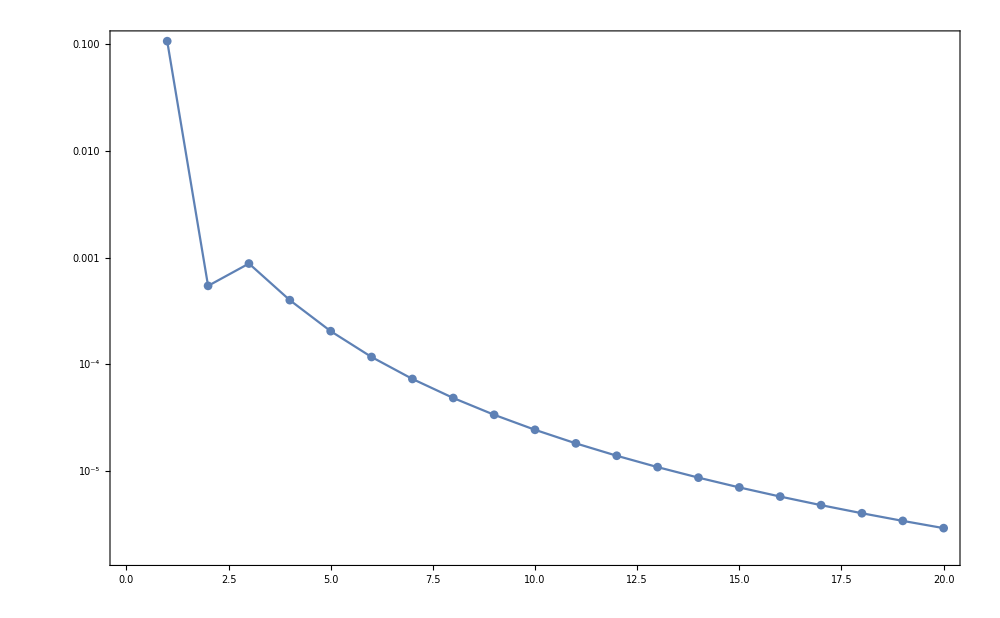

```mathematica
ListLogPlot[Abs@((enV2-energyVs1)/enV2),Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_energyVs1.mx",energyVs1];
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_energyVs1.mx"];
```

```mathematica
δVs1=δ50[Vs1[r,a,c1]]
Abs@(δ50V-δVs1)
```

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031974411274343923108171900826125583966156808585) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.899447) is less than WorkingPrecision (50.).

End with 1.0625098s

End with 1.0625098s

{1/1000000,-0.031963521468805168951407653582893111822793127131699}    1.06251

{0.001,-0.73250972518451946268338186943172750864515004353146}    1.06251

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112859777687179151567103296995576489017535799) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 1.2031236s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22752) is less than WorkingPrecision (50.).

{1/1000000000,-0.0010112856330217658849817416730032025654856716863463}    1.203124

End with 1.3749994s

{0.01,-0.88718535566223301858893957674218801654496318248869}    1.390625

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095975017477786582932894714851538097579286333) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==2166.41) is less than WorkingPrecision (50.).

End with 1.1249979s

End with 1.1249979s

{1/100000,-0.10061880961453922280409682164587106083568314853747}    1.124998

{0.003,1.570334734540060653538857719220635706175587028986}    1.140623

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031979623249957195393675877937599320027701491573) is less than WorkingPrecision (50.).

End with 1.2343860s

{1/100000000,-0.003197951423248455936166130758749183000658101352336}    1.250018

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.208106) is less than WorkingPrecision (50.).

End with 1.5781399s

{0.03,-0.20517728044782776685401233769788077247729227751695}    1.57814

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31379108518803959850096946052871183417339295728) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.1875106s

{1/10000,-0.30406065560809848060691236605000827032716632431204}    1.203136

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0162092) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 1.2968868s

{0.007,0.01620781381215011975697054122903875219118620143578}    1.312512

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010112695201574110295672900467416044632208952389) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.2343802s

{1/10000000,-0.010112350492392546062533989012234237098394315540821}    1.23438

FindRoot::precw: The precision of the argument function (Tan[δ]==0.802736) is less than WorkingPrecision (50.).

End with 1.5468888s

{0.07,0.67640688100641043228248135618838835835946765894288}    1.562514

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.582456) is less than WorkingPrecision (50.).

End with 1.6718908s

{0.3,0.52741936708656395447753373050247467192818865957894}    1.687516

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.7519865860681476893754782966431330431718586040208 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.154708) is less than WorkingPrecision (50.).

End with 1.8750185s

{0.1,-0.15349072532099535676571779250673423883035965927701}    1.875019

FindRoot::precw: The precision of the argument function (Tan[δ]==6.1806539204956404001604686908681203608975519112) is less than WorkingPrecision (50.).

End with 3.0469029s

{1,1.4103911880918314606344528034270163710116103327053}    3.06253

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.05111) is less than WorkingPrecision (50.).

End with 2.7187784s

{0.7,-1.1171654844730205383288859788550441300667953577499}    2.7344

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.19276327145344873538631488415808884396665493498) is less than WorkingPrecision (50.).

End with 4.8594329s

{3,-0.19042758244849480667815363041465528717892656272499}    4.875045

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.0129173940368399755999130890980557434134606519) is less than WorkingPrecision (50.).

End with 9.2188534s

{7,-1.1097189108342283555731198952664542570497603542276}    9.2500878

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.45769050876847382387026043486415308484667399) is less than WorkingPrecision (50.).

End with 7.1563197s

{10,-1.417162484401406685841026891969190285174263323832}    7.1875799

{-0.0010112856330217658849817416730032025654856716863463,-0.003197951423248455936166130758749183000658101352336,-0.010112350492392546062533989012234237098394315540821,-0.031963521468805168951407653582893111822793127131699,-0.10061880961453922280409682164587106083568314853747,-0.30406065560809848060691236605000827032716632431204,-0.73250972518451946268338186943172750864515004353146,1.570334734540060653538857719220635706175587028986,0.01620781381215011975697054122903875219118620143578,-0.88718535566223301858893957674218801654496318248869,-0.20517728044782776685401233769788077247729227751695,0.67640688100641043228248135618838835835946765894288,-0.15349072532099535676571779250673423883035965927701,0.52741936708656395447753373050247467192818865957894,-1.1171654844730205383288859788550441300667953577499,1.4103911880918314606344528034270163710116103327053,-0.19042758244849480667815363041465528717892656272499,-1.1097189108342283555731198952664542570497603542276,-1.417162484401406685841026891969190285174263323832}

{4.37506673405945689977473688568240420242×10^-13,1.5218735879595550621805274915081253368855×10^-11,4.85647325580679101767376851130706432607789×10^-10,1.5375635009368198196256756868844596807691×10^-8,4.8758676281436554279289040316971452977000004×10^-7,0.0000157314158320873495936875305992890247869582618,0.0003235570590751702364695303484830158918574327317,0.000367427029743407540721823520990022686832948609,0.000349699390394969255843896696379011554043304905057,0.0004311982768586620099088444543945599829248351027,0.0020933642132265750349883386718249775444804285181,0.0055223372399496383481347319060275069237513689753,0.00806473827739106737770959483825349209307103329714,0.0321446044803837767687497705588952801115987557198,0.0771959188075152180439881702239205117908865131121,0.10340086411700177687481860752307872203788443845,0.20194223602608080751155712302664501925180743637149,0.2579505568872989517273296613110989980181241417448,0.271041227031474438961450312357819918598155757649}

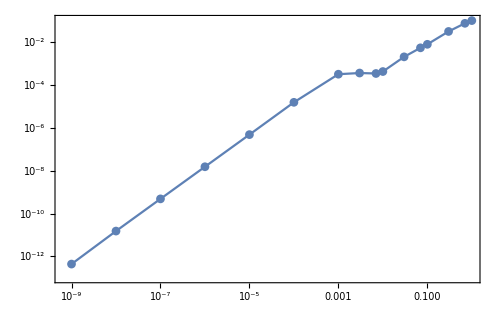

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs@(δ50V-δVs1)}],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->500]
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
δexpminus9=δ50e[ee[[2]],V2[r,Fc,Fd]]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112859773312107943129835816740420171167336579) is less than WorkingPrecision (50.).

End with 0.2499891s

-0.0010112856325842592115757959830257288769174312661043

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->200,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

FindRoot::precw: The precision of the argument function ({Tan[δ]==-0.00031979675285863811032093311326522213716570452313}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

End with 0.9146458s

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00078871263141617024602877422370586475283010401903) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.9136469s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

End with 0.9446691s

End with 0.7945598s

End with 0.8696137s

End with 0.8826232s

End with 0.8185800s

End with 0.8095718s

End with 1.0807643s

End with 1.1117839s

End with 0.6374601s

End with 0.7845560s

End with 0.6484595s

End with 0.7775471s

{-36.2848343037296749841314493522,5.84107887879535486384182660827,0.000048355729,0.00015291427}

End with 0.6604664s

End with 0.7815525s

End with 0.7165182s

End with 0.8285727s

End with 0.6644708s

End with 0.7685435s

End with 0.7845543s

End with 0.8536148s

End with 0.7745473s

End with 0.7735459s

{-36.2773104769008042182447563365,5.4832596718278800714886469878,4.6706502×10^-6,0.000014769897}

End with 0.8005657s

End with 0.7845552s

End with 0.8045672s

End with 0.8125750s

End with 0.7945622s

End with 0.8486628s

End with 0.8180898s

End with 0.8170786s

End with 0.8716148s

End with 0.8891636s

End with 0.8656114s

End with 0.8906296s

{-36.6834395456917120380262783012,5.14175548476832075126495307148,3.9755068×10^-6,0.00001257166}

End with 0.8516014s

End with 0.9036366s

End with 0.8536041s

End with 0.9276556s

End with 0.8856243s

End with 0.8996358s

End with 0.7775475s

End with 0.8666119s

End with 0.7815525s

End with 0.8526015s

{-38.6553118643845328103239736804,3.48575257426452906541756366496,-3.9502253×10^-6,-0.000012491712}

End with 0.7725442s

End with 0.8846332s

End with 0.7915566s

End with 0.8886283s

End with 0.7745391s

End with 0.9566759s

End with 0.8876273s

End with 0.8826240s

End with 0.8676124s

End with 0.9246512s

{-40.3824766302601902016884272563,2.16518428824345869448582602056,-2.5342888×10^-6,-8.014127×10^-6}

End with 0.9306587s

End with 0.8826363s

End with 0.9426672s

End with 0.8526008s

End with 0.9072055s

End with 0.9196491s

End with 0.7260146s

End with 0.7335169s

End with 0.7290153s

End with 0.7310019s

{-40.1855763726514885487436933159,2.33663080565194298108536368548,-2.9281776×10^-8,-9.2597158×10^-8}

End with 0.7550344s

End with 0.7135035s

End with 0.7290572s

End with 0.7034981s

End with 0.7325156s

End with 0.7235127s

End with 0.7675347s

End with 0.7835542s

End with 0.7435247s

End with 0.7601523s

{-40.0033000889068549529081435988,2.47582213010597573394342520013,-2.8891795×10^-8,-9.1363902×10^-8}

End with 0.7535330s

End with 0.7535323s

End with 0.7695435s

End with 0.7975634s

End with 0.8115736s

End with 0.7421437s

End with 0.7145160s

End with 0.7305027s

End with 0.7084998s

End with 0.7064988s

{-40.0056606871827451565768013917,2.47426668331494072209597412745,-1.2875964×10^-12,-4.0717421×10^-12}

End with 0.7265248s

End with 0.7475280s

End with 0.7615395s

End with 0.7125034s

End with 0.7295263s

End with 0.7305293s

End with 0.7385095s

End with 0.7045106s

End with 0.7535339s

End with 0.7195061s

{-40.0056363754438506361480877729,2.47428529180625853235536884301,-5.1649793×10^-16,-1.6333103×10^-15}

End with 0.7435227s

End with 0.7295165s

End with 0.7235106s

End with 0.7165058s

End with 0.7235110s

End with 0.7295145s

End with 0.7445277s

End with 0.7345166s

End with 0.7075006s

End with 0.7285131s

{-40.005636375465796741644941689,2.47428529179394579077616222375,4.9976912×10^-28,1.580408×10^-27}

End with 0.7335177s

End with 0.7074998s

End with 0.7024955s

End with 0.7645382s

End with 0.7675421s

End with 0.7461309s

End with 0.7505414s

End with 0.7295149s

End with 0.7585364s

End with 0.7205087s

{-40.0056363754657967416369804012,2.47428529179394579078224790683,-6.8133217×10^-39,-2.154561×10^-38}

{-40.0056363754657967416369804012,2.47428529179394579078224790683}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_c2d1.mx",{c2,d1}];
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.49332,-0.182142,-0.0703483,-0.037147,-0.0229264,-0.0155491,-0.0112354,-0.00849648,-0.00664954,-0.00534542,-0.00439048,-0.00367033,-0.00311387,-0.00267499,-0.00232276,-0.00203579,-0.00179889,-0.00160106,-0.00143415,-0.00129204}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$21905]-u''[r$21905]/2==e$21904 u[r$21905],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.49332462808832754778386566545,-0.182142476216508676359308591496,-0.0703482651472945188721391542754,-0.0371469591597168021789085770145,-0.0229263710377710836496972320414,-0.0155491492149864901386111180801,-0.0112353764350299599537772718745,-0.00849648047933151199415389640898,-0.00664954491556984113713700335206,-0.00534541713066330993468445875391,-0.00439047737629807789781456437769,-0.00367033213483557378120736410422,-0.00311386858488095988952264548058,-0.00267499276323362504295649395252,-0.00232276432707585848266475093181,-0.0020357886794829857502006321525,-0.00179888908781754351499938118569,-0.00160105775000575047045392784932,-0.00143415340973243268784085605281,-0.00129205008026020202068872398371}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_energyVs2.mx",energyVs2];
```

```mathematica
EigenEnergySolo[Vs2[r,a ,{c2,d1}],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-0.02306137918729334],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->1000}]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-13.5226570746494407817962716474 Power[«2»]-135.115464425549849306990459068 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$280155]-u''[r$280155]/2==e$280154 u[r$280155],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0230613826550219397933054205879}

```mathematica
energyVs2[[5]]=First@%80
```

-0.0230613826550219397933054205879

```mathematica
energyVs2
```

{-1.49332462808832754778386566545,-0.182142476216508676359308591496,-0.0703482651472945188721391542754,-0.0371469591597168021789085770145,-0.0229263710377710836496972320414,-0.0155491492149864901386111180801,-0.0112353764350299599537772718745,-0.00849648047933151199415389640898,-0.00664954491556984113713700335206,-0.00534541713066330993468445875391,-0.00439047737629807789781456437769,-0.00367033213483557378120736410422,-0.00311386858488095988952264548058,-0.00267499276323362504295649395252,-0.00232276432707585848266475093181,-0.0020357886794829857502006321525,-0.00179888908781754351499938118569,-0.00160105775000575047045392784932,-0.00143415340973243268784085605281,-0.00129205008026020202068872398371}

```mathematica
Abs@((energyVs2-enV2)/enV2)
```

{0.1605691623098750529126893072,0.00652366646683163632780177901,0.00039766200765740596813256615,0.00007375477748259882779229056,0.00002131066181383321931911537,7.93209842178515910006447×10^-6,3.48502033773451123709741×10^-6,1.7221881003115137165811×10^-6,9.2922284478976545728775×10^-7,5.3678414240852173998779×10^-7,3.2747708439162710380916×10^-7,2.0890801678281752662801×10^-7,1.383232434239417137788×10^-7,9.451923923469338361276×10^-8,6.635617895439581866658×10^-8,4.768912564837483409226×10^-8,3.498380023219374257372×10^-8,2.61324590923006682725×10^-8,1.98375908160237073816×10^-8,1.52777601813422069517×10^-8}

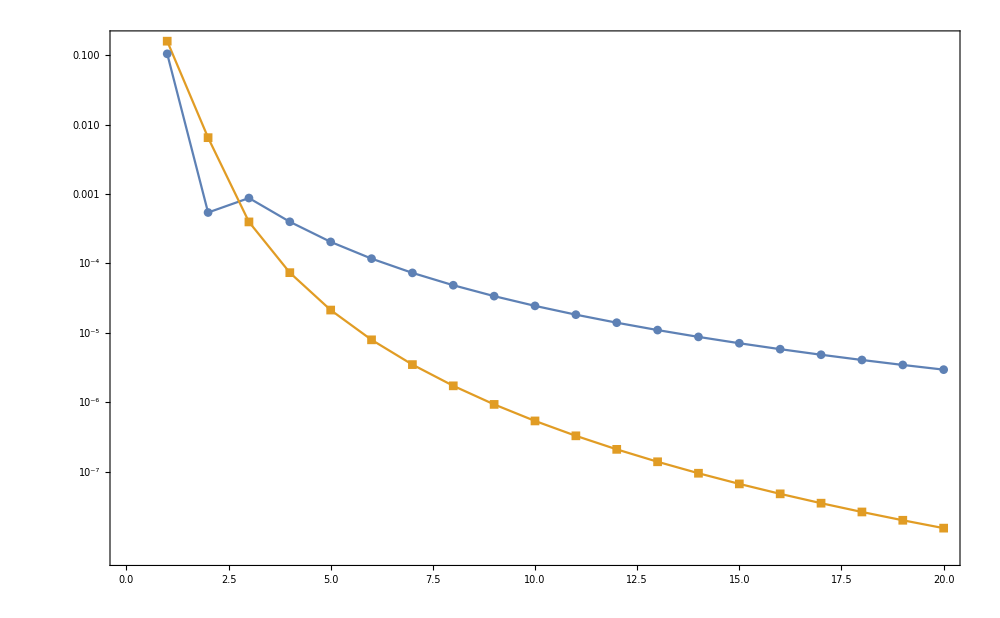

```mathematica
ListLogPlot[{Abs@((energyVs1-enV2)/enV2),Abs@((energyVs2-enV2)/enV2)},Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
Abs@(δ50V-δVs2)
```

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112859773312107943129835816740420386623653037) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.898865) is less than WorkingPrecision (50.).

End with 0.9374959s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031974395883050705426232984912379424622690450691) is less than WorkingPrecision (50.).

End with 0.9374959s

{1/1000000000,-0.0010112856325842592115757959830257288984630408772188}    0.9374959

End with 0.9843717s

{0.001,-0.73218745058089974715806242017870510381965052030736}    0.9531238

NDSolve::precw: The precision of the differential equation ({{2 (1/100000000+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/1000000,-0.031963506093231361103866716682938661981770793226977}    0.9843717

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22648) is less than WorkingPrecision (50.).

End with 1.3281244s

{0.01,-0.88677047682358315547520180553183352112240159580136}    1.328124

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095925763775311118200316969106504627974602767) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031979623097768285633569827201770980974779303102) is less than WorkingPrecision (50.).

End with 0.9062591s

End with 0.9687598s

{1/100000,-0.10061832204720127844559972794159136160130369881142}    0.921884

FindRoot::precw: The precision of the argument function (Tan[δ]==10153.6) is less than WorkingPrecision (50.).

{1/100000000,-0.0031979514080297206015984468142487706962302134266204}    0.9843853

NDSolve::precw: The precision of the differential equation ({{2 (1/10000+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 1.0312573s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.003,1.5706978391566117914615688801104359546075621258885}    1.031257

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31377381174789701405898423224068955349582518322) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010112694715877310779033020447369192179660142372) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.9531468s

End with 0.9687602s

{1/10000,-0.30404493045726474854703119612923424631115950058489}    0.9531468

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.206148) is less than WorkingPrecision (50.).

{1/10000000,-0.010112350006745412026765451261553048303034519037852}    0.9687602

End with 1.7187666s

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0165496) is less than WorkingPrecision (50.).

{0.03,-0.20330006526116496898354978822567788168208238013615}    1.718767

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.1250131s

NDSolve::precw: The precision of the differential equation ({{2 (1+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.007,0.016548109171738373179512434925965159631409337588226}    1.140636

NDSolve::precw: The precision of the differential equation ({{2 (7+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.809982) is less than WorkingPrecision (50.).

End with 1.7500149s

{0.07,0.68079815412931310530281199580115364582560064048821}    1.76564

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.604964) is less than WorkingPrecision (50.).

End with 1.9843976s

{0.3,0.54406132289389165287667941552596316793234968539324}    2.000019

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.148629) is less than WorkingPrecision (50.).

End with 3.0469037s

{0.1,-0.1475492889147355794825672015520683789977773627965}    3.046904

FindRoot::precw: The precision of the argument function (Tan[δ]==7.6011785304348786530121955235308262261958995042) is less than WorkingPrecision (50.).

End with 4.7969215s

{1,1.439988984342654046010471785817333335775858129443}    4.812546

NDSolve::precw: The precision of the differential equation ({{2 (3+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.91836) is less than WorkingPrecision (50.).

End with 3.7656617s

{0.7,-1.0902709599890907444756950652606455618054738686585}    3.781286

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.16099762816145399676447492798582254693803565634) is less than WorkingPrecision (50.).

End with 8.7500830s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.8874650105219060052604721170555410936863998152) is less than WorkingPrecision (50.).

{3,-0.1596278368783251787074098763126402226299743765289}    8.781333

End with 13.5001271s

{7,-1.0835851974378885963440560266318232719600224384673}    13.562628

NDSolve::precw: The precision of the differential equation ({{2 (10+2.54010331134145277760946256476 Power[«2»]-2.47428529179394579078224790683 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-5.585873482298788123390924075768219241599381315) is less than WorkingPrecision (50.).

End with 16.1564026s

{10,-1.3936498583745608962136033289546095319285858790512}    16.218903

{-0.0010112856325842592115757959830257288984630408772188,-0.0031979514080297206015984468142487706962302134266204,-0.010112350006745412026765451261553048303034519037852,-0.031963506093231361103866716682938661981770793226977,-0.10061832204720127844559972794159136160130369881142,-0.30404493045726474854703119612923424631115950058489,-0.73218745058089974715806242017870510381965052030736,1.5706978391566117914615688801104359546075621258885,0.016548109171738373179512434925965159631409337588226,-0.88677047682358315547520180553183352112240159580136,-0.20330006526116496898354978822567788168208238013615,0.68079815412931310530281199580115364582560064048821,-0.1475492889147355794825672015520683789977773627965,0.54406132289389165287667941552596316793234968539324,-1.0902709599890907444756950652606455618054738686585,1.439988984342654046010471785817333335775858129443,-0.1596278368783251787074098763126402226299743765289,-1.0835851974378885963440560266318232719600224384673,-1.3936498583745608962136033289546095319285858790512}

{2.15456096111145×10^-38,5.4502786667730486261065336544314×10^-19,1.9154491056401669566233534663610482×10^-16,6.120152065725935680241900357447378628×10^-14,1.9424870007045699186123470480150320274×10^-11,6.26499835528971251760982526500878013453464×10^-9,1.282455455454711150081095460611066357909508×10^-6,4.3224131922696180106626311897742548578517066×10^-6,9.404030806715833302002999452604113820168752611×10^-6,0.000016319438208798896171073244040064560363248415,0.0002161490265637771645257891996220867492705311373,0.00113106411704696532780409229326221945761838743,0.0021233018711312900945590038835876322604887368166,0.0155026486730560783696040855354067841074377299055,0.0503013943235854241907972566295219435295650240206,0.07380306786617919149879962513276175727363664171,0.17114249045591117954081336892462995470285525017539,0.2318168434909591924982657926764680129283862259845,0.247528601004628649334026749343239165352478312868}

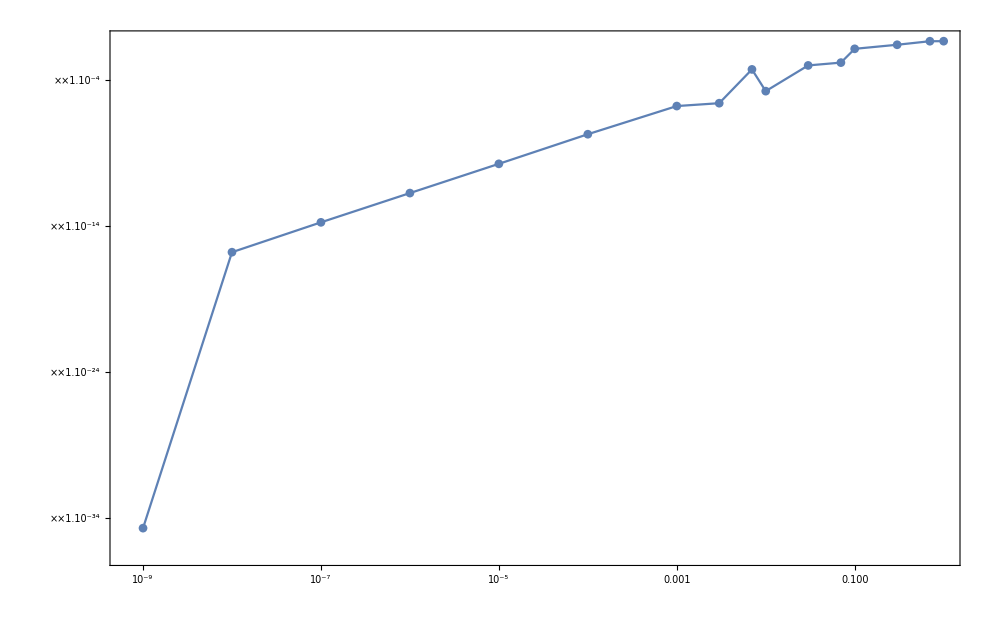

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs@(δ50V-δVs2)}],Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

## Matrix element <p^4>

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_energyVs1.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_c1.mx"]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_energyVs2.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_c2d1.mx"]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_efV2.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_efVs2.mx"]
```

```mathematica
nRange=20;
```

```mathematica
AbsoluteTiming[efV2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V2[r,Fc,Fd],enV2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.0001];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-1.28671748016823998683246939937 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0371496991275094971376871216291 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0112354155906817963792443540493 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00534542000000000044804497862288 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00439047881407927901570550355666 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0229268596243229908242861347373 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00849649511189428805344001023526 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.183338515542431527686387767079 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00367033290159754118667384782054 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0155492725533467704478200973264 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00664955109448462572903939845956 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0703762511086017671933385949847 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00311386901560142172482786082609 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00232276448120563406646016825862 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00179888915074952220468132047761 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00143415343818258176190046376664 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00267499301607192988019323757218 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00203578877656797250950195440884 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00160105779184532772026119297082 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-0.99895352636201278972478862820538575868617674167672 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00129205009999983359076539824947 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1605.56,{7.91406976033×10^-1345                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.17525878916×10^-472                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],6.8362×10^-270                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.20025×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.95995×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.47678×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.29908×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.39756×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.9085×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.08791×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.79525×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.0000156969                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],90.5724                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.92796×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],8.13706×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.88859×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0186002                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2851.63                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.28856×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-6.38815×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

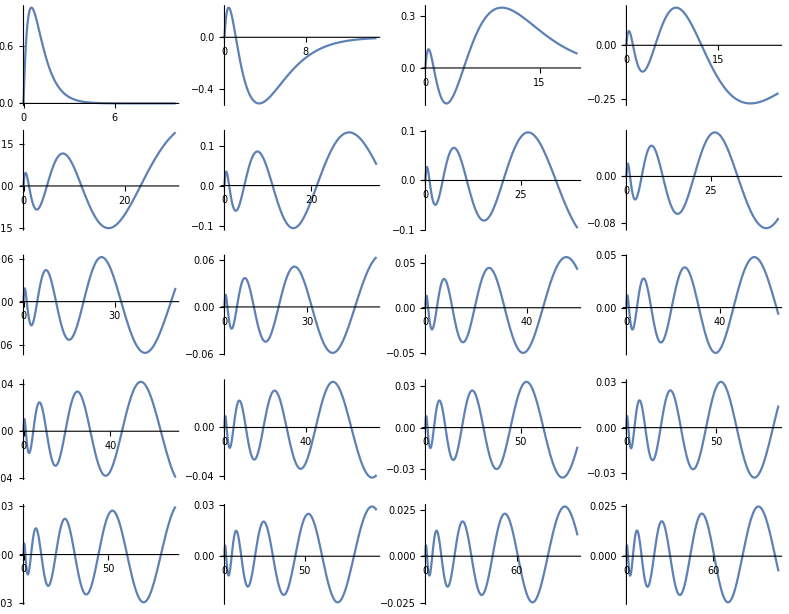

```mathematica
GraphicsGrid@Partition[Table[Plot[efV2[[n]],{r,0,5+5n},ImageSize->Small,AxesOrigin->{0,0},PlotRange->Full],{n,1,20}],4]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_efV2.mx",efV2];
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.49332462808832754778386566545 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0371469591597168021789085770145 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112353764350299599537772718745 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534541713066330993468445875391 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00439047737629807789781456437769 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229263710377710836496972320414 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00849648047933151199415389640898 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.182142476216508676359308591496 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367033213483557378120736410422 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155491492149864901386111180801 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00664954491556984113713700335206 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0703482651472945188721391542754 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00311386858488095988952264548058 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232276432707585848266475093181 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00179888908781754351499938118569 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143415340973243268784085605281 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267499276323362504295649395252 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0020357886794829857502006321525 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160105775000575047045392784932 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.54010331134145277760946256476 Power[«2»]+2.47428529179394579078224790683 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00129205008026020202068872398371 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1616.82,{1.05304189389×10^-1452                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.36969107924×10^-471                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],7.9577×10^-270                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.22533×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.98356×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.47895×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.30148×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.39984×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.90873×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.08828×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.79531×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.0000156973                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],90.5736                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.92799×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],8.13712×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.88861×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0186003                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2851.64                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.28856×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-6.38816×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_efVs2.mx",efVs2];
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,If[n>15,4000,b]},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,If[n>15,4000,b]},opt]+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
Plot[Evaluate@D[efV2[[1]],{r,2}],{r,0,10^-40},PlotRange->All]
```

-Graphics-

```mathematica
NIntegrate[D[efV2[[1]],{r,2}]^2,{r,10^-20,2000}]
```

NIntegrate::precw: The precision of the argument function (6.26325001714×10^-2689 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«54495»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (MachinePrecision).

68.8868

```mathematica
REAL=Table[NIntegrate[D[efV2[[n]],{r,2}]^2,{r,10^-20,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,nRange}];
N[%,6]
REF=Table[NIntegrate[D[efV2[[n]],{r,2}]^2,{r,10^-20,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,nRange-2,nRange}];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (6.26325001714×10^-2689 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«54495»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.913440278439727007493775524209105900660847196444720895331183474719191832731075997266647083662333435×10^-20}. NIntegrate obtained 68.88682868572038899525815497756520358644046567171573761454769148013754411579844265685535099943486298 and 7.274643854456575598298395770813534828524880347139637221988498390659798764421817111751070338859056196×10^-18 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (1.38123322149×10^-944 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«20847»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {3.581690855485564757481580304972130636981672853160637950228299586697453790233916317606055037857715356×10^-20}. NIntegrate obtained 5.495025535074949730736023531795857308996665327829130136405912575731766517596570249309720041267496744 and 7.567105407497662644266822400778220436277954669869236753146987577100618730801545060871583880446394703×10^-20 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (4.67336894748063×10^-539 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«14601»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.223361304170680963283765193375827625255965335168752897710313626698443022091858640730212563174020307×10^-20}. NIntegrate obtained 1.307701454211381074958185951287904207733557550642658185065071784018224808232342259177036724760206333 and 4.274285028789044440229191726248987156563419063648238942723702209190479488874231085742649267480225563×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.03906145010955400430124600831411727611517461354981160527157684510723195961641331164634383403498797069 and 1.127177272168356588584182135031101701998839045809087843689215699828185522413243776996080418948008475×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.008109603799852301118212921003862963224984131219138565692968064786464865739591172052198706254130863788 and 6.697668936470909399826803463646040433762192080059601643218820717827043482151647059401818341341741245×10^-23 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.006657555617320395498083009575601326140198290940138226931066057203960945866119654777486730126279932634 and 5.924008635119025742673843478903807908875090578846100451850354990155887393334464258062645051274848359×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{68.8868,5.49503,1.3077,0.50658,0.247203,0.138675,0.0854409,0.0563177,0.0390615,0.0281934,0.0210108,0.0160749,0.0125715,0.0100166,0.0081096,0.00665756,0.00553247,0.00464727,0.00394127,0.00337133}

NIntegrate::precw: The precision of the argument function (8.1318×10^6 («1»)^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.004647266689507136239297044360752088360288457446655157878770681893386553128450321360147657511696373344 and 5.56090153155335454670975349672554653410291497723560882453798952626605131499201178849164953614438033×10^-23 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (1.66039×10^16 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},«43»,{48,47},{49,48},{50,49},«10611»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.003941270205040512082148449223335443573198914515224432025668666448983301959449310400336706897602112834 and 1.547988940000268240057900347471154927556046539658505571395029967920630618404200714717873566831210188×10^-22 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (4.08084×10^-15 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,4000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},«43»,{48,47},{49,48},{50,49},«11833»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.003371332511191128242517492553291759910062582724684201600029898452363668253117355885535324938968053719 and 4.882843839300282310952543940106454553617515345208638153409777234192701388423090576481764356298636823×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.00464727,0.00394127,0.00337133}

### Matrix element in V_eff^(a^2)

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000138504158273109948804989145348 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

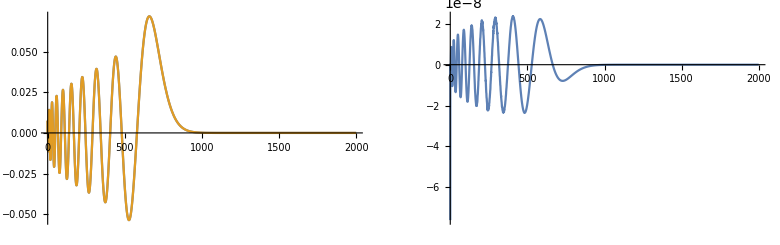
{316.214,-Graphics-}

```mathematica
AbsoluteTiming@Module[{n=19},ef=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{4000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
ef=If[OddQ[n],ef,-ef];
GraphicsGrid@{{Plot[{ef,r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium],
Plot[{ef-r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium]}}
]
```

```mathematica
NIntegrate[(D[ef,{r,2}])^2,{r,1.*10^-50,4000},Exclusions->50]
Abs@((%-REAL[[20]])/REAL[[20]])
```

0.00103203

0.0517522

```mathematica
AbsoluteTiming[efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0500078698243863935055737602971 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00312500761726746385913647922606 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00102040862718159308244150419666 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00050000007796292676973750649047 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000413223188903938793994512264818 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000781250237936304904722289140259 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00200000249550536888652531039438 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000347222253552894523182159148667 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000617284082651037569419393087846 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00138888989166308326560993291706 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000295858009162576239009167422901 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000222222232488422260934584517289 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000173010386113415734680628773593 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000255102055311667723228331312929 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0125002441801421361773951351802 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000195312507434709104520394621199 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000138504158273109948804989145348 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00555558766918009791462567717346 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000154320991780025227507069598258 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000125000002436179368929957388996 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{2445.63,{8.41457014008×10^-818                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-5.480197172726×10^-380                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],8.39339×10^-233                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.14087×10^-158                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],3.44212×10^-113                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.2177×10^-82                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.63894×10^-60                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.11706×10^-43                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.11448×10^-30                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.23154×10^-19                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.02554×10^-10                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.00340555                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],9183.21                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-3.3482×10^9                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.39999×10^14                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.12086×10^-31                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],4.58687×10^-24                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-1.70214×10^-17                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],1.40823×10^-11                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-3.21204×10^-6                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
Module[{n=14,efunction},
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]];
efVs1[[n]]=efunction[[n]]
]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_efVs1_3rd.mx",efVs1];
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,If[#>15,4000,2000]},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (7.08049906424×10^-1635 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},«37»,{45,44},{46,45},{47,46},{48,47},{49,48},{50,49},«33464»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4623668815636586952048333778507701378928326188347611607266528355568406087082334849813321133116737352}. NIntegrate obtained 4.24775143448205958754880454950146237906635095041566811870478274004760680511885743899799314631144069 and 9.4294993357277365201116231630111112705893449190092986268406862750987694486421162445050224791268157×10^-20 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (3.0032561052×10^-759 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4659802004911373337071412325364140666142675879536833723647658789795401373362383226469339285990687524}. NIntegrate obtained 0.7174212809199777929012894664292984532181745825076807971498109279693081909549759755618068069181562719 and 3.633547634066690580084017448059494709124396188637866489408592955265507683293373880163695855550865649×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (7.04490049372286×10^-465 («1»)^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4876851693547784171767109075724296318712432966469218138641756757990863061327905245533927872319965803}. NIntegrate obtained 0.2310293704005218476208680659105967534842423940550152647074475234522278493705018614045060625254064782 and 1.565100318490618058414719654037227888225773080342227279351087081435626816539107499249587825522316916×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.01984903187431712853938055156973597616852240651017562336163919592199692943063748185718615390076255168 and 2.074762998997241455182522314947624539621804802400464589855355901814498606670080863891670931669490639×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0134018318956914725368765651229453202777814174071243471793431669035110112443153993803885775000156491 and 1.349272075646587028220132847748484682868033567759296291558026803594026509245122889347926101283489337×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.009469642671235533884112092422123566763653524626848019889082198752430783453376630716086874204278076897 and 9.499293015886584565705581065264491615077331817953452020612324005259862951024457468747029254543415047×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{4.24775,0.717421,0.231029,0.101363,0.053096,0.0311892,0.019849,0.0134018,0.00946964,0.00693668,0.00523211,0.0040432,0.00318883,0.00255916,0.00208492,0.00172097,0.00143703,0.00121227,0.00103203,0.000885825}

{0.15045,0.11702,0.108887,0.105207,0.103108,0.101751,0.100801,0.1001,0.0995605,0.0991327,0.0987853,0.0984974,0.098255,0.098048,0.0978694,0.0977135,0.0975763,0.0974547,0.0973461,0.0972486}

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,If[#>15,4000,2000]][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{(*15,*)20})==(REF[[#]]&/@{(*2,*)3})](*/.Z->1*),{γ,-1,-10},WorkingPrecision->50,AccuracyGoal->10,PrecisionGoal->10,MaxIterations->10000]
((p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{15,20})-(REF[[#]]&/@{2,3}))/(REF[[#]]&/@{2,3})/.RESVs1
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.000885825 and 1.79075×10^-9 for the integral and error estimates.

FindRoot::precw: The precision of the argument function ({0.000885825+0.000282618 γ==157/160000}) is less than WorkingPrecision (50.).

{γ→0.33764725954412159015702246610372791534324179410807}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.000885825 and 1.79075×10^-9 for the integral and error estimates.

{1.02139,9.66804×10^-17}

```mathematica
p4Vs1=p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (7.08049906424×10^-1635 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},«37»,{45,44},{46,45},{47,46},{48,47},{49,48},{50,49},«33464»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (3.0032561052×10^-759 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.558842}. NIntegrate obtained 0.00838342 and 0.0000125049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.00172097 and 3.23177×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.00143703 and 2.82697×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{5.01942,0.813096,0.259336,0.113299,0.0592056,0.0347244,0.0220751,0.0148931,0.0105169,0.00770014,0.00580569,0.004485,0.00353632,0.00283738,0.00231112,0.00190735,0.00159242,0.00134317,0.00114333,0.00098125}

{0.00388414,0.000734028,0.000295047,0.000156002,0.0000949686,0.0000629033,0.0000440104,0.0000319552,0.0000237978,0.0000180236,0.0000137876,0.0000105888,8.11453×10^-6,6.20316×10^-6,4.50098×10^-6,3.31483×10^-6,2.25921×10^-6,1.37747×10^-6,6.32936×10^-7,0.}

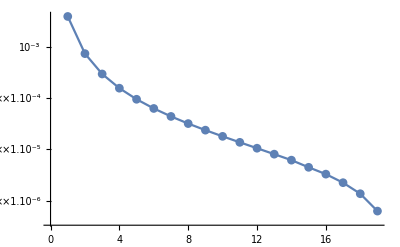

```mathematica
ListLogPlot[%161,Joined->True,PlotMarkers->{Automatic}]
```

### Matrix element in V_eff^(a^4)

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSEVs2)/REAL);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (1.10889723029×10^-2904 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},«45»,{48},{49},«58394»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.8672848747069103788248656614030491635086096602341699376841091507198513584990437379047903649958575371}. NIntegrate obtained 5.914787130094658143699491117078696897715770597698401714739499291343986523363934182393334183032743181 and 1.951709780220112267768681390250985994923018994622458951850477815582512447372603192524078987249089048×10^-17 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (4.0572964445×10^-941 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},«45»,{48},{49},«20253»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.674909050366569263930343810822164750647999259272294724080536910337801942353497925386762522290094541 and 9.998564895135604036947630790405343592193254093257614844717138395584263823753003546643547845335834692×10^-22 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (6.33250363763365×10^-539 («1»)^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.617859897344484778095054927575697841947499404880792682469840218960577908609575220951478753305860582}. NIntegrate obtained 0.4309000958108418298853265874122440843536648682301012810379489485385949209451589125203631935102170535 and 5.183443448400555359519764027811514308485887952056996331712914817968834957175093902694042204291451218×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.5488159957370418318191587144004307005349291114843399616863025521027547726762374175130359548247295072}. NIntegrate obtained 0.1708660848668242544344596382085622441231737394069451119932159119799903955028763776218446225189256621 and 1.043755663819795578943048580390460845176659928301372730127951182263702199097651200341358557765894592×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.08444123010254753751580098532627684908439410227321198509121816590903636914203507999034383157316016899 and 4.842999476183892135244426724873832039362934934182730667753505226951326600640315632627932841444220667×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.01958270754980600346765373625310437286179793065976903990018149582854259962853630036405880359811087497 and 2.397754497180126467479001672584438541019366864006395884471647055699773268721498987470047927028319278×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{5.91479,1.67491,0.4309,0.170866,0.0844412,0.0477529,0.029587,0.0195827,0.0136255,0.00985921,0.00736244,0.00564234,0.00441893,0.00352512,0.00285699,0.00234758,0.00195242,0.0016412,0.00139276,0.00119204}

{0.914138,0.695195,0.67049,0.662706,0.658413,0.65565,0.653714,0.652282,0.651178,0.650301,0.649588,0.648996,0.648497,0.648071,0.647702,0.647381,0.647098,0.646846,0.646622,0.64642}

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{18,19,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->10,PrecisionGoal->10]
```

NIntegrate::precw: The precision of the argument function (8.13184×10^6 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{1},{1},{2},{3},{4},{5},«39»,{45},{46},{47},{48},{49},«11212»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001641199715206312304477323229092907178616660174876777394389093293954857163693703575838459947150758148 and 6.129410134832923675867564004950867300801431871047267331230597710394705445801740003328092200490826398×10^-23 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (516320. ⅇ^(-r^2/2) («1»)^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.5926995055025836787488566821374677509489174917475930566908741752117556829636822757077887984880243951}. NIntegrate obtained 2.345917741874906029020159859461974438628465226791386663908759085664460923370599828255628808654632802×10^-6 and 1.772312574987995849244688527085673810582705584526805173133961176577360531927988069071556587366201457×10^-30 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (8.13184×10^6 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{1},{1},{2},{3},{4},{5},«39»,{45},{46},{47},{48},{49},«11212»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.5926995641528945051112997335712917515848389884473570834527803365030104642861795746178366820129587344}. NIntegrate obtained -3.063861283995008231488651599619314726462483213827289033560808637602518950888191092438585794606283666×10^-6 and 2.658636877474967790022751430503746605672126736395358992826711959762684530718761496790440212080521277×10^-29 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001392759015086082003722433792453979042134279380482150579224404274145915361548804917623523972541803656 and 1.065310862162760927361658213541734004317250433651743152373899260956556315223327928744772281776279959×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {3.028040569938218487689145840253995365288074576875644684353298192895640452208226514635044360871729942}. NIntegrate obtained 1.988676041546726048535478945516829682246807574288146168340092051556692449963185310901047123667299886×10^-6 and 1.979693326533830481861605737142477559842014723655880229296103189033757226636187005081440935337904365×10^-29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001192035525345078004331839420521082590634399029535963680117171498581323438263641051894568700621059968 and 9.642801279011063665895946208742672097253784913275490492900901520177853220516361876144048547901921038×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{Z→0.99918520949538239350076711918217763140346993424471,γ→175.53285953927434520045793172286821727545429579638,η→-847.17234828114513182209087741004168649971120977207}

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (1.10889723029×10^-2904 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},«45»,{48},{49},«58394»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.8672848747069103788248656614030491635086096602341699376841091507198513584990437379047903649958575371}. NIntegrate obtained 5.914787130094658143699491117078696897715770597698401714739499291343986523363934182393334183032743181 and 1.951709780220112267768681390250985994923018994622458951850477815582512447372603192524078987249089048×10^-17 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (7.04079170286×10^-2906 ⅇ^(-r^2/2) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},«45»,{48},{49},«58394»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.8672853339012739531712873588893960641064335410894042538497609050195805783124526938476769414088376303}. NIntegrate obtained 0.03758755591423616770487777380720987395605226282454931621493290907938372984785262048746880386212647813 and 5.113376477083449152439846535199326389717527310925796626776683682084216862598435313086204015187125194×10^-24 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (1.10889723029×10^-2904 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},«45»,{48},{49},«58394»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.8672853339012739531712873588893960641064335410894042538497609050195805783124526938476769414088376303}. NIntegrate obtained -0.08067902323939071406574925966515272131140636266979070541720345079362868678842068820147833926958468344 and 1.129336194213618103952237153595082259893743830648165671964824574821052605700302510912989105182458768×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.674909050366569263930343810822164750647999259272294724080536910337801942353497925386762522290094541 and 9.998564895135604036947630790405343592193254093257614844717138395584263823753003546643547845335834692×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.08444123010254753751580098532627684908439410227321198509121816590903636914203507999034383157316016899 and 4.842999476183892135244426724873832039362934934182730667753505226951326600640315632627932841444220667×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.01958270754980600346765373625310437286179793065976903990018149582854259962853630036405880359811087497 and 2.397754497180126467479001672584438541019366864006395884471647055699773268721498987470047927028319278×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{80.8569,5.30215,1.30428,0.506286,0.247155,0.138664,0.0854375,0.0563166,0.039061,0.0281932,0.0210107,0.0160748,0.0125715,0.0100166,0.0081096,0.00665755,0.00553247,0.00464727,0.00394127,0.00337133}

{0.173764,0.0350999,0.00261821,0.000580203,0.000194454,0.0000816238,0.0000393229,0.0000206999,0.0000115387,6.66219×10^-6,3.91197×10^-6,2.3004×10^-6,1.3303×10^-6,7.39311×10^-7,3.81166×10^-7,1.70227×10^-7,5.41623×10^-8,0.,0.,0.}

## ψ_0 in effective theory

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
REALψ0=NLimit[efV2[[#]]/(r √(4π)),r->0]&/@Range@nRange
REF=NLimit[efV2[[#]]/(r √(4π)),r->0]&/@{19,20};
```

{1.50007,0.382981,0.183652,0.113506,0.0789867,0.0590165,0.0462469,0.037501,0.0312026,0.0264894,0.022854,0.0199803,0.0176622,0.0157601,0.0141765,0.0128414,0.0117035,0.0107242,0.00987431,0.00913101}

```mathematica
FALSEψ0=NLimit[efVs2[[#]]/(√(4π)r),r->0,Scale->10]&/@Range@nRange
N[%,6]
Abs@((REALψ0-FALSEψ0)/REALψ0);
N[%,6]
```

{0.527261,0.189773,0.0918285,0.0567248,0.039459,0.0294763,0.0230954,0.0187262,0.0155802,0.0132262,0.0114107,0.00997571,0.00881818,0.00786841,0.0070777,0.0064111,0.00584294,0.00535402,0.00492967,0.00455857}

{0.527261,0.189773,0.0918285,0.0567248,0.039459,0.0294763,0.0230954,0.0187262,0.0155802,0.0132262,0.0114107,0.00997571,0.00881818,0.00786841,0.0070777,0.0064111,0.00584294,0.00535402,0.00492967,0.00455857}

{0.648508,0.504484,0.499988,0.500248,0.500434,0.500541,0.500606,0.500648,0.500677,0.500697,0.500712,0.500723,0.500731,0.500738,0.500744,0.500748,0.500752,0.500755,0.500758,0.50076}

```mathematica
ψ0True[n_,d_][γ_,η_,{optpsi___}]:=√(4π)(γ NIntegrate[efVs2[[n]]/r δa[r] r^2,{r,0,d},optpsi]+η a^2 NIntegrate[efVs2[[n]]/r Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,d},optpsi])
```

```mathematica
RES=FindRoot[Thread[ψ0True[#,2000][γ,η,{MaxRecursion->20}]&/@{19,20}==(REF[[#]]&/@{1,2})],{{γ,0,-2},{η,0,-2}},AccuracyGoal->10,MaxIterations->100000,WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function ({2 √π (-0.0000201202 γ-0.000610036 η)==0.00987431,2 √π (-0.0000186137 γ-0.00056405 η)==0.00913101}) is less than WorkingPrecision (30.).

{γ→-28.6399447715517295568244924157,η→-3.62151257210345593630664727548}

```mathematica
ψ0Vs1=ψ0True[#,If[#>15,4000,2000]][γ,η,{MaxRecursion->20}]&/@Range@nRange/.RES;
N[%,6]
Abs@((REALψ0-ψ0Vs1)/REALψ0);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (6.68614586343×10^-1454 «2» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},«27»,{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«58394»},{«1»}}}][r]) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (-4.04434846399×10^-472 «2» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},«27»,{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«20253»},{«1»}}}][r]) is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-3.40551,0.369117,0.182963,0.113401,0.0789614,0.0590086,0.0462439,0.0374997,0.031202,0.0264891,0.0228539,0.0199802,0.0176622,0.0157601,0.0141765,0.0128414,0.0117035,0.0107242,0.00987431,0.00913101}

{3.27024,0.0362008,0.00375542,0.000921315,0.000319794,0.000134639,0.0000639419,0.0000328668,0.0000178035,9.96403×10^-6,5.676×10^-6,3.23961×10^-6,1.82489×10^-6,9.94719×10^-7,5.10482×10^-7,2.2955×10^-7,8.14831×10^-8,1.12823×10^-8,1.39539×10^-9,1.3919×10^-9}